```mathematica
SetDirectory[NotebookDirectory[]];
<<MaTeX`
```

HO Results

## HO fidelity final

```mathematica
STA=Import["./Global_Output/tHO_U0=2417.82_L=200_gamma=10_sumTerms=8_numComps=1_00/fidelities_exp_a=2418_Tf=var_alpha=0_d=0_STA.dat"]
```

```mathematica
STA={{"#tfinal","#cabs2_fidelity_sta","#cabs2_fidelity_sq_sta"},{1.,0.9999668,0.9999336},{5.,0.9999671,0.9999342},{10.,0.9999671,0.9999342},{20.,0.9999671,0.9999342},{50.,0.9999671,0.9999341},{75.,0.9999669,0.9999337},{100.,0.999967,0.999934},{150.,0.9999669,0.9999338},{200.,0.9999671,0.9999342},{250.,0.9999669,0.9999338},{300.,0.999967,0.999934},{350.,0.9999671,0.9999342},{400.,0.9999669,0.9999338},{450.,0.9999671,0.9999341},{500.,0.999967,0.999934},{600.,0.9999671,0.9999342},{700.,0.999967,0.999934},{800.,0.9999669,0.9999338},{900.,0.999967,0.999934},{1000.,0.9999671,0.9999341},{1250.,0.999967,0.9999341},{1500.,0.999967,0.999934},{1750.,0.999967,0.999934},{2000.,0.9999671,0.9999341},{3000.,0.9999667,0.9999334},{4000.,0.9999675,0.9999351},{5000.,0.9999662,0.9999323},{6000.,0.9999681,0.9999363},{7000.,0.9999654,0.9999308},{8000.,0.999969,0.999938},{9000.,0.9999641,0.9999282},{10000.,0.9999706,0.9999412},{12500.,0.9999659,0.9999318},{15000.,0.9999598,0.9999195},{17500.,0.9999573,0.9999146},{20000.,0.9999672,0.9999345}};
```

```mathematica
Adiabatic=Import["./Global_Output/tHO_U0=2417.82_L=200_gamma=10_sumTerms=8_numComps=1_00/fidelities_exp_a=2418_Tf=var_alpha=0_d=0_adiabatic.dat"]
```

```mathematica
Adiabatic={{"#tfinal","#cabs2_fidelity_adiabatic#cabs2_fidelity_sq_adiabatic"},{1.,0.2023713,0.04095414},{5.,0.3089237,0.09543386},{10.,0.349063,0.121845},{20.,0.4091972,0.1674424},{50.,0.5049638,0.2549884},{75.,0.5492364,0.3016607},{100.,0.5819235,0.338635},{150.,0.6293316,0.3960582},{200.,0.6635503,0.440299},{250.,0.6901933,0.4763668},{300.,0.711899,0.5068002},{350.,0.7301284,0.5330874},{400.,0.7457774,0.556184},{450.,0.7594363,0.5767436},{500.,0.7715144,0.5952345},{600.,0.7920349,0.6273193},{700.,0.8089316,0.6543703},{800.,0.8231664,0.6776029},{900.,0.8353649,0.6978345},{1000.,0.8459578,0.7156446},{1250.,0.8672708,0.7521586},{1500.,0.8834619,0.780505},{1750.,0.8962937,0.8033423},{2000.,0.906794,0.8222753},{3000.,0.9347094,0.8736816},{4000.,0.9508417,0.9041},{5000.,0.9612276,0.9239586},{6000.,0.9684643,0.937923},{7000.,0.9738401,0.9483646},{8000.,0.9779203,0.9563281},{9000.,0.981007,0.9623747},{10000.,0.9834024,0.9670803},{12500.,0.9879551,0.9760552},{15000.,0.9908424,0.9817687},{17500.,0.9925924,0.9852396},{20000.,0.9938156,0.9876695}};
```

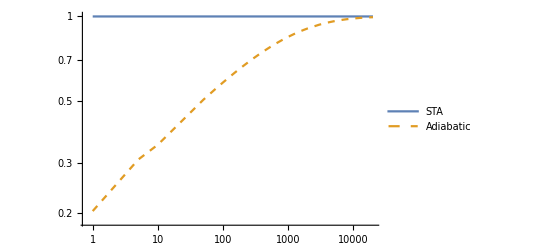

```mathematica
ListLogLogPlot[{
Table[{STA[[i,1]],STA[[i,2]]},{i,2,Length[STA]}]
,
Table[{Adiabatic[[i,1]],Adiabatic[[i,2]]},{i,2,Length[Adiabatic]}]
}
,PlotRange->All
,PlotLegends->{"STA","Adiabatic"}
,PlotStyle->{,Dashed,}
,Joined->True
,ImageSize->400
]
```

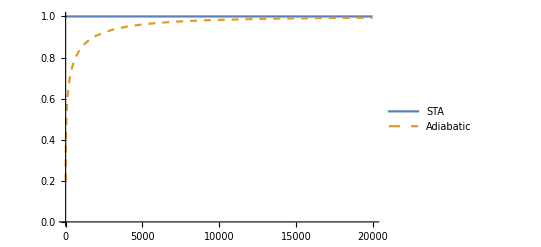

```mathematica
ListLinePlot[{
Table[{STA[[i,1]],STA[[i,2]]},{i,2,Length[STA]}]
,
Table[{Adiabatic[[i,1]],Adiabatic[[i,2]]},{i,2,Length[Adiabatic]}]
}
,PlotRange->All
,PlotLegends->{"STA","Adiabatic"}
,PlotStyle->{,Dashed,}
,ImageSize->400
]
```

```mathematica
(* here I'm scaling to make units nice on plot *)
```

```mathematica
adls=Table[{Adiabatic[[i,1]],Adiabatic[[i,2]]},{i,2,Length[Adiabatic]}]
```

{{1.,0.202371},{5.,0.308924},{10.,0.349063},{20.,0.409197},{50.,0.504964},{75.,0.549236},{100.,0.581924},{150.,0.629332},{200.,0.66355},{250.,0.690193},{300.,0.711899},{350.,0.730128},{400.,0.745777},{450.,0.759436},{500.,0.771514},{600.,0.792035},{700.,0.808932},{800.,0.823166},{900.,0.835365},{1000.,0.845958},{1250.,0.867271},{1500.,0.883462},{1750.,0.896294},{2000.,0.906794},{3000.,0.934709},{4000.,0.950842},{5000.,0.961228},{6000.,0.968464},{7000.,0.97384},{8000.,0.97792},{9000.,0.981007},{10000.,0.983402},{12500.,0.987955},{15000.,0.990842},{17500.,0.992592},{20000.,0.993816}}

```mathematica
nm=Interpolation[adls]
```

InterpolatingFunction[{{1., 20000.}}, <>]

```mathematica
Solve[nm[t]==0.99,t]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{t→14136.1}}

```mathematica
Solve[nm[t]==0.9,t]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{t→1833.28}}

```mathematica
om0=250*2.0*Pi;
Solve[om0*rt==14136.055782272719,rt]
```

{{rt→8.99929}}

```mathematica
om0*8.999292614285892
```

14136.1

```mathematica
Solve[om0*rt==1833.2846088799226,rt]
```

{{rt→1.16711}}

```mathematica
adscaled=Table[{Adiabatic[[i,1]]/om0,Adiabatic[[i,2]]},{i,2,Length[Adiabatic]}]
```

{{0.00063662,0.202371},{0.0031831,0.308924},{0.0063662,0.349063},{0.0127324,0.409197},{0.031831,0.504964},{0.0477465,0.549236},{0.063662,0.581924},{0.095493,0.629332},{0.127324,0.66355},{0.159155,0.690193},{0.190986,0.711899},{0.222817,0.730128},{0.254648,0.745777},{0.286479,0.759436},{0.31831,0.771514},{0.381972,0.792035},{0.445634,0.808932},{0.509296,0.823166},{0.572958,0.835365},{0.63662,0.845958},{0.795775,0.867271},{0.95493,0.883462},{1.11408,0.896294},{1.27324,0.906794},{1.90986,0.934709},{2.54648,0.950842},{3.1831,0.961228},{3.81972,0.968464},{4.45634,0.97384},{5.09296,0.97792},{5.72958,0.981007},{6.3662,0.983402},{7.95775,0.987955},{9.5493,0.990842},{11.1408,0.992592},{12.7324,0.993816}}

plot

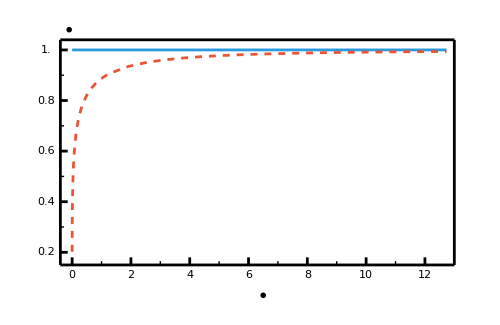

```mathematica
classColour=RGBColor[1, 0, 0];
minAnharmColour=RGBColor[0, 0.6, 0];
polyColour=RGBColor[0, 0, 0.6];

classColour=RGBColor[0.915, 0.3325, 0.2125];
minAnharmColour=RGBColor[0.16, 0.6, 0.2];
polyColour=RGBColor[0.16, 0.6, 0.88];

(*** Plot window ***)
xMin=0.0;xMax=13.0;
yMin=0.15;yMax=1.0;
(*** Frame window offsets ***)
xoffset=0.4;
yoffset=0.04;
xoffsetRight=0;

aspectRatio=0.65;
imageSize=500;

fontSize=18;
matexMag=2;
gridThickness=0.0001;

axesThickness=0.004;
plotThickness=0.004;

tickMajorThickness=0.004;
tickMinorThickness=tickMajorThickness/2;

yLabelOffset=0.03;
yLabelSteps=0.1;
yTickMajorList=Table[i,{i,0.2,1.0,0.2}];
ytickMajorLength=0.25;
yTickMinorList=Table[i,{i,0.3,0.9,0.2}];
ytickMinorLength=ytickMajorLength/2;

xTickMajorList=Table[i,{i,0,13,2}];
xtickMajorHeight=0.03;
xTickMinorList=Table[i,{i,1,13,2}];
xtickMinorHeight=xtickMajorHeight/2;
xLabelSteps=Length[xTickMajorList];

lighterVal=0.0;
dVal=0.5;

numSum=4;
plotOutputsinSq=
ListLinePlot[{
Table[{Adiabatic[[i,1]]/om0,1},{i,2,Length[STA]}]
,
adscaled
(*,
eSTA1storder1comp
,
eSTA2ndorder8comp*)
}
,PlotRange->{{xMin,xMax},{yMin,yMax}}
,PlotStyle->{
(*,{polyColour,Thickness[plotThickness]}
,{classColour,Thickness[plotThickness]}*)
{polyColour, Thickness[plotThickness]}
,{classColour,Thickness[plotThickness],Dashed}
}
,BaseStyle->{FontSize->fontSize,FontFamily->"Latin Modern Roman"}
,Frame->False
,Axes->False
];

frame=Graphics[{
(*** Dashed F=1 Line ***)
{
(*{AbsoluteDashing[6],Line[{{xMin,1},{xMax,1}}]}*)
}
,
(*** Frame ***)
{
Thickness[axesThickness]
,Line[{{xMin-xoffset,yMin},{xMax+xoffsetRight,yMin}}]
,Line[{{xMax+xoffsetRight,yMin},{xMax+xoffsetRight,yMax+yoffset}}]
,Line[{{xMax+xoffsetRight,yMax+yoffset},{xMin-xoffset,yMax+yoffset}}]
,Line[{{xMin-xoffset,yMax+yoffset},{xMin-xoffset,yMin}}]
}
,
{
(*** Ticks Major ***)
Thickness[tickMajorThickness],
(* x-axis *)Table[Line[{{i,yMin},{i,yMin+xtickMajorHeight}}],{i,xTickMajorList}]
,
(* y-axis *)Table[Line[{{xMin-xoffset,i},{xMin-xoffset+ytickMajorLength,i}}],{i,yTickMajorList}]
}
,
{
(*** Ticks Minor ***)
Thickness[tickMinorThickness],
(* x-axis *)Table[Line[{{i,yMin},{i,yMin+xtickMinorHeight}}],{i,xTickMinorList}]
,
(* y-axis *)Table[Line[{{xMin-xoffset,i},{xMin-xoffset+ytickMinorLength,i}}],{i,yTickMinorList}]
}
,
{
(*** Tick Major values ***)
(* x-axis *)Table[Inset[i,{i,yMin-0.04}],{i,xTickMajorList}]
,
(* y-axis *)Table[Inset[i,{xMin-0.9,i}],{i,yTickMajorList}]
}
,
{
(*** Axes labels ***)
(* x-axis *)Inset[MaTeX["t_f \:(\\text{s)}",Magnification->matexMag],{(1.xMax-xMin)/2+xMin,yMin-0.12}]
,
(* y-axis *)Inset[MaTeX["F",Magnification->matexMag],{xMin-0.1,yMax+0.08}]
}
}
,BaseStyle->{FontSize->fontSize,FontFamily->"Latin Modern Roman"}
,LabelStyle->{FontSize->fontSize,FontFamily->"Latin Modern Roman",Black}
,AspectRatio->aspectRatio
,ImageSize->imageSize];

mainPlotsinSq0=Show[frame,plotOutputsinSq]
```

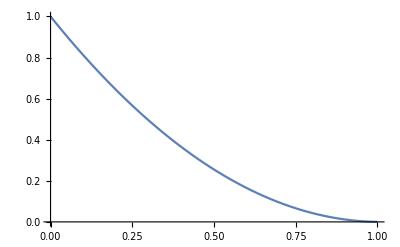

```mathematica
om0=1;
omf=0.01;
tf=1;
om[t_]=om0+(omf-om0)t/tf;
Plot[om[t]^2,{t,0,tf}]
```

```mathematica
plotL=Table[{t,om[t]^2},{t,0,1,0.01}];
```

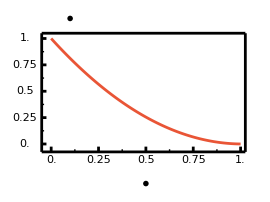

```mathematica
classColour=RGBColor[0.915, 0.3325, 0.2125];
minAnharmColour=RGBColor[0.16, 0.6, 0.2];
polyColour=RGBColor[0.16, 0.6, 0.88];

(*** Plot window ***)
xMin=0;xMax=1.0;
yMin=-0.075;yMax=1.0;

yMin0=-0.1;yMax0=1.1;
(*** Frame window offsets ***)
xoffset=0.05;
yoffset=0.05;
xoffsetRight=5;

aspectRatio=0.75;
imageSize=270;
ratio=500/imageSize;

fontSize=16;
matexMag=2;
gridThickness=0.0001;

axesThickness=ratio*0.004;
plotThickness=ratio*0.004;

tickMajorThickness=ratio*0.004;
tickMinorThickness=tickMajorThickness/2;

yLabelOffset=0.0;
yTickMajorList=Table[i,{i,{0,0.25,0.5,0.75,1.0}}];
ytickMajorLength=0.025;
yTickMinorList=Table[i,{i,{0.125,0.375,0.625,0.875}}];
ytickMinorLength=ytickMajorLength/2;

xTickMajorList=Table[i,{i,0.0,1.0,0.25}];
xtickMajorHeight=0.05;
xTickMinorList=Table[i,{i,0.125,1.0,0.25}];
xtickMinorHeight=xtickMajorHeight/2;
xLabelSteps=Length[xTickMajorList];

plotOutputsinSq=
ListLinePlot[
plotL
,PlotRange->{{1,xMax},{yMin,yMax}}
,PlotStyle->{
{classColour,Thickness[plotThickness]}
,{classColour,Thickness[plotThickness],AbsoluteDashing[{7.5,5}]}
,{polyColour,Thickness[plotThickness]}
,{classColour,Thickness[plotThickness]}
}
,BaseStyle->{FontSize->fontSize,FontFamily->"Latin Modern Roman"}
,Frame->False
,Axes->False
];

frame=Graphics[{
(*** Dashed F=1 Line ***)
{
(*{minAnharmColour,Thickness[plotThickness],DotDashed,Line[{{xMin,0},{30,0}}]}*)
}
,
(*** Frame ***)
{
Thickness[axesThickness]
,Line[{{xMin-xoffset,yMin},{xMax+xoffset/2,yMin}}]
,Line[{{xMax+xoffset/2,yMin},{xMax+xoffset/2,yMax+yoffset}}]
,Line[{{xMax+xoffset/2,yMax+yoffset},{xMin-xoffset,yMax+yoffset}}]
,Line[{{xMin-xoffset,yMax+yoffset},{xMin-xoffset,yMin}}]
}
,
{
(*** Ticks Major ***)
Thickness[tickMajorThickness],
(* x-axis *)Table[Line[{{i,yMin},{i,yMin+xtickMajorHeight}}],{i,xTickMajorList}]
,
(* y-axis *)Table[Line[{{xMin-xoffset,i},{xMin-xoffset+ytickMajorLength,i}}],{i,yTickMajorList}]
}
,
{
(*** Ticks Minor ***)
Thickness[tickMinorThickness],
(* x-axis *)Table[Line[{{i,yMin},{i,yMin+xtickMinorHeight}}],{i,xTickMinorList}]
,
(* y-axis *)Table[Line[{{xMin-xoffset,i},{xMin-xoffset+ytickMinorLength,i}}],{i,yTickMinorList}]
}
,
{
(*** Tick Major values ***)
(* x-axis *)Table[Inset[i,{i,yMin-0.075}],{i,Drop[xTickMajorList,1]}]
,Inset[0.,{0,yMin-0.075}]
,
(* y-axis *)Table[Inset[1.0*i,{xMin-0.14,i}],{i,yTickMajorList}]
}
,
{
(*** Axes labels ***)
(* x-axis *)Inset[MaTeX["t / t_f",Magnification->matexMag],{0.5,yMin-0.3}]
,
(* y-axis *)Inset[MaTeX["\\omega_a^{2} / \\omega_0^2",Magnification->matexMag],{xMin+0.1,yMax+0.14+yoffset}]
}
}
,BaseStyle->{FontSize->fontSize,FontFamily->"Latin Modern Roman"}
,LabelStyle->{FontSize->fontSize,FontFamily->"Latin Modern Roman",Black}
,AspectRatio->aspectRatio
,ImageSize->imageSize
];

mainPlotsinSqInset0=Show[frame,plotOutputsinSq]
```

```mathematica
exportPlot=Show[
mainPlotsinSq0,
(*** Inset Plot ***)
Epilog->
{
Inset[mainPlotsinSqInset0,{8.8,0.55}]
}]
```

-Graphics-

```mathematica
Export["open_trap_adiabatic.pdf",exportPlot]
```

open_trap_adiabatic.pdf